```mathematica
<< Toolbox`
<< Toolbox`Style`
<< XML`
SetDirectory[NotebookDirectory[]];
<< util`
bigg2equilibrator = Import["../data/bigg2equilibratorViaKEGG.m.gz"];
```

# iAB-RBC-238

## SBML2MODEL

### Import model from SBML and translate to MASSmodel

#### Flux Bounds

```mathematica
getReferenceFluxesAndBoundsFromXML[path_String]:=Block[{tmp,tmp2,tmp3,tmp4},
tmp=Import[path,"Text"];
tmp2=StringCases[tmp,RegularExpression["(?s)listOfReactions.+"]];
tmp3=Flatten[StringSplit[tmp2,RegularExpression["<reaction id="]][[1]][[2;;]]];
tmp4=StringCases[#,RegularExpression["(?s)^(\"R_.+?\").+\"LOWER_BOUND\"\\s*?value=\"([-e\\d\\.]+)\".+?\"UPPER_BOUND\"\\s*?value=\"([-e\\d\\.]+)\".+?\"FLUX_VALUE\"\\s*?value=\"(.+?)\""]:>N[{"$1"->{ToExpression@StringReplace["$2","e"->"*10^"],ToExpression@StringReplace["$3","e"->"*10^"],ToExpression@StringReplace["$4","e"->"*10^"]}}]]&/@tmp3;
Flatten[tmp4]/.s_String:>StringReplace[s,{"\""->""}]
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
iABrefBounds=#[[1]]->#[[2,1;;2]]&/@(getReferenceFluxesAndBoundsFromXML["../data/iAB-RBC-238/1752-0509-5-110-s5.xml.gz"]//.s_String:>StringReplace[s,biggCommonStringReplacements]);
```

#### GPR

```mathematica
protAssoc=Flatten[Thread[#[[1]]->(If[StringMatchQ[#,RegularExpression[".*\\+.*"]],proteinComplex[Sequence@@(protein/@StringSplit[#,RegularExpression["\\s*\\+\\s*"]])],protein[#]]&/@StringSplit[#[[2]],RegularExpression["\\s*,\\s*"]])]&/@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[1]][[2;;,{1,-5}]],{_,"''"}]];
```

```mathematica
protAssoc//Length
protAssoc//Union//Length
```

784

777

```mathematica
protAssoc=Union[protAssoc];
```

#### Elemental composition

```mathematica
bigg2inchi=Import["/Users/niko/work/Code/Mixed/Chemoinformatics199/Mappings/bigg2inchi/bigg2inchi.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
elementalComposition=str2mass[#[[1]]]->formula2elementalComposition[#[[4]]]&/@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[2]],{"","","",""}][[2;;]];
```

```mathematica
stuff=Rule@@@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[1]],{"","","",""}][[2;;]][[All,{1,3}]];
```

```mathematica
stuff[[1]]
```

2KMBTA→[c] : 2kmb + glu-L <==> akg + met-L

#### Build model

```mathematica
SetDirectory[NotebookDirectory[]];
rbcReactions=(sbml2model["../data/iAB-RBC-238/1752-0509-5-110-s5.xml.gz", Method->"Light"])["Reactions"]//.s_String:>StringReplace[s,biggCommonStringReplacements];
stuff=Rule@@@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[1]],{"","","",""}][[2;;]][[All,{1,3}]]/.s_String:>StringTrim[s];
correctRev=#[[1]]->If[!StringMatchQ[#[[1]],RegularExpression["^sink.*"]],StringMatchQ[#[[2]],RegularExpression[".*<==>.*"]],True]&/@stuff;
correctedRbcReactions=ReplacePart[#,-1->getID[#]/.correctRev]&/@rbcReactions;
correctRxnsAndBounds=Table[
	bnds=getID[rxn]/.iABrefBounds;
	If[!reversibleQ[rxn],Switch[bnds,{a_/;a<0,b_/;b<=0},Reverse@rxn->Abs[Reverse[bnds]],{a_/;a<0,b_/;b>0},Print["Encountered negative bound for irreversible reaction:"<>getID[rxn]];rxn->{0,bnds[[2]]},_,rxn->bnds],rxn->(bnds)]
	,{rxn,correctedRbcReactions}
];
rbc=constructModel[correctRxnsAndBounds[[All,1]],Constraints->(getID[#[[1]]]->#[[2]]&/@correctRxnsAndBounds),Ignore->{m["h",_],m["h2o",_]},"ReorderStoichiometry"->False,"UnitChecking"->True];
updateNotes[rbc,defaultInitializationNotes[]<>"\n This model covers the iAB-RBC-238 reconstruction by Aarash Bordbard."];
setGPR[rbc,protAssoc];
setID[rbc,"iAB-RBC-238"];
setElementalComposition[rbc,elementalComposition];
dg=Quiet[calcDeltaG[rbc["Reactions"],bigg2equilibrator,is->0.25 Mole Liter^-1,pH->7.3],{calcDeltaG::missingPseudoisomerData}];
Print["Proportion of reactions without thermodynamic information."];
Count[dg,r_Rule/;r[[2]]===Undefined]/N@Length[rbcᵀ]
keq=dG2keq[DeleteCases[dg,r_Rule/;r[[2]]===Undefined]];
keq=Quiet[adjustUnits[keq,rbc,DefaultAmountUnit->Mole],{adjustUnits::noUnitsProvidedKeq}];
updateParameters[rbc,keq]
```

Encountered negative bound for irreversible reaction:ALAt4

Proportion of reactions without thermodynamic information.

0.343284

```mathematica
DeleteCases[stripUnits@dg[[All,2]],Undefined]//Length
```

308

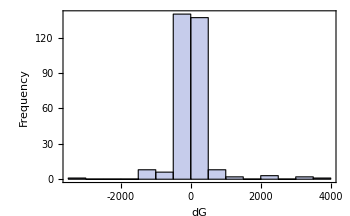

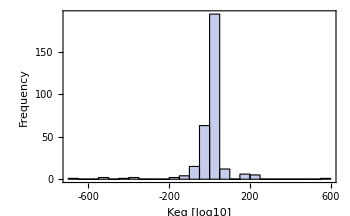

```mathematica
Histogram[DeleteCases[stripUnits@dg[[All,2]],Undefined],FrameLabel->{"dG","Frequency"}]
Histogram[Log[10,stripUnits@FilterRules[rbc["Parameters"],_Keq][[All,2]]],FrameLabel->{"Keq [log10]","Frequency"}]
```

```mathematica
stoichiometricallyConsistentQ[rbc]
```

True

```mathematica
elementallyBalancedQ@rbc
```

True

```mathematica
rbc["Fluxes"]//Length
rbc["Fluxes"]//Union//Length
rbc["Proteins"]//Union//Length
```

469

469

347

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238.m.gz",rbc]
```

../models/iAB-RBC-238/iAB-RBC-238.m.gz

```mathematica
getNotes@rbc
```

Model constructed on Tue 30 Apr 2013 16:07:53 by niko on staphylococcus.ucsd.edu using Mathematica 9.0 for Mac OS X x86 (64-bit) (November 20, 2012) at the following geodetic location: latitude 32.88; longitude -117.24
 This model covers the iAB-RBC-238 reconstruction by Aarash Bordbard.

### Visualize model

```mathematica
(*currencyMets=annotateCurrencyMetabolites[getReactions@rbc];
SetDirectory[NotebookDirectory[]];
Export["../Data/iAB-RBC-238/currencyMetsRBC.m.gz",currencyMets];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
currencyMets=Import["../Data/iAB-RBC-238/currencyMetsRBC.m.gz"];
```

```mathematica
net=pathwaytize[DeleteCases[reactions2bipartite[getReactions[rbc],AliasingRules->currencyMets],r_Rule/;MemberQ[r,m_metabolite/;StringMatchQ[getID[m],RegularExpression[".*\\$.*"]],∞]],10,Method->"Remove"];
(*net=DeleteCases[reactions2bipartite[getReactions[rbc],AliasingRules->currencyMets],r_Rule/;MemberQ[r,m_metabolite/;StringMatchQ[getID[m],RegularExpression[".*\\$.*"]],∞]];*)
connComponents=ConnectedComponents@Graph[Union[(Rule@@Sort[List@@#]&/@net)]/.r_Rule:>UndirectedEdge@@r];
nets=Cases[net,r_Rule/;MemberQ[#,Alternatives@@r]]&/@Sort[connComponents,Length[#1]>Length[#2]&];
transp=Cases[Union@Cases[nets,r_Rule/;MemberQ[r,metabolite[_,"e"],∞],∞],_String,2];
```

```mathematica
SlideView[visualizePathways[DeleteCases[#,r_Rule/;MemberQ[transp,r[[1]]]||MemberQ[transp,r[[2]]]||MemberQ[r,s_String/;StringMatchQ[s,RegularExpression[".*DM_.*"]]||StringMatchQ[s,RegularExpression[".*sink_.*"]],∞]],
PlotFunction->LayeredGraphPlot,ImageSize->1200,EdgeRenderingFunction->({If[EuclideanDistance[#1[[1]],#1[[-1]]]>5,Unevaluated[Sequence[Gray,Dotted]],Black],Arrow[#1,0.1]}&)]&/@nets[[1;;2]]]
```

### Visualize GPRs

```mathematica
SlideView[visualizeGPR[#]&/@gpr2graphs[rbc["GPR"]],AppearanceElements->All]
```

## Translate SB2 book models to iAB-RBC-238

```mathematica
sb2MetsToiAB={metabolite["glu",comp_]:>metabolite["glc-D",comp],metabolite["gap",comp_]:>metabolite["g3p",comp],metabolite["phos",comp_]:>metabolite["pi",comp],metabolite["pg13",comp_]:>metabolite["13dpg",comp],metabolite["dpg23",comp_]:>metabolite["23dpg",comp],metabolite["pg3",comp_]:>metabolite["3pg",comp],metabolite["pg2",comp_]:>metabolite["2pg",comp],metabolite["lac",comp_]:>metabolite["lac-L",comp],metabolite["gl6p",comp_]:>metabolite["6pgl",comp],metabolite["go6p",comp_]:>metabolite["6pgc",comp],metabolite["ru5p",comp_]:>metabolite["ru5p-D",comp],metabolite["x5p",comp_]:>metabolite["xu5p-D",comp],metabolite["gssg",comp_]:>metabolite["gthox",comp],metabolite["gsh",comp_]:>metabolite["gthrd",comp],metabolite["ado",comp_]:>metabolite["adn",comp],metabolite["ino",comp_]:>metabolite["ins",comp],metabolite["hyp",comp_]:>metabolite["hxan",comp]};
```

### Glycolysis

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../models/SB2/glycolysis.m.gz"];
```

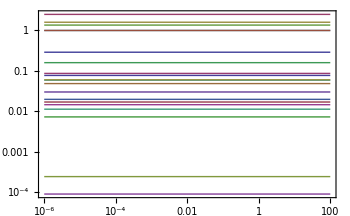

```mathematica
plotSimulation[simulate[glycolysis,{t,0,100}][[1]]]/.m:$MASS$speciesPattern:>ToString[m]
```

```mathematica
sb2ToiAB={"vhk"->"HEX1","vpgi"->"PGI","vpfk"->"PFK","vtpi"->"TPI","vald"->"FBA",
"vgapdh"->"GAPD","vpgk"->"PGK","vpglm"->"PGM","veno"->"ENO","vpk"->"PYK",
"vldh"->"LDH_L","vamp"->Missing["NotAvailable"],"vapk"->"ADK1",
"vpyr"->Missing["NotAvailable"],"vlac"->Missing["NotAvailable"],
"vatp"->Missing["NotAvailable"],"vnadh"->Missing["NotAvailable"],
"vgluin"->Missing["NotAvailable"],"vampin"->Missing["NotAvailable"],"vh"->Missing["NotAvailable"],"vh2o"->Missing["NotAvailable"]
};
```

```mathematica
TableForm[{Cases[glycolysis["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(atp^c+(glc-D)^c⇌adp^c+g6p^c+h^c)^vhk | (atp^c+(glc-D)^c→adp^c+g6p^c+h^c)^HEX1
(g6p^c⇌f6p^c)^vpgi | (g6p^c⇌f6p^c)^PGI
(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^vpfk | (atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK
(dhap^c⇌g3p^c)^vtpi | (dhap^c⇌g3p^c)^TPI
(fdp^c⇌dhap^c+g3p^c)^vald | (fdp^c⇌dhap^c+g3p^c)^FBA
(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^vgapdh | (g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD
((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^vpgk | ((3pg)^c+atp^c⇌(13dpg)^c+adp^c)^PGK
((3pg)^c⇌(2pg)^c)^vpglm | ((2pg)^c⇌(3pg)^c)^PGM
((2pg)^c⇌h2o^c+pep^c)^veno | ((2pg)^c⇌h2o^c+pep^c)^ENO
(adp^c+h^c+pep^c⇌atp^c+pyr^c)^vpk | (adp^c+h^c+pep^c→atp^c+pyr^c)^PYK
(h^c+nadh^c+pyr^c⇌(lac-L)^c+nad^c)^vldh | ((lac-L)^c+nad^c⇌h^c+nadh^c+pyr^c)^LDH_L
(amp^c⇌∅)^vamp | —
(2 adp^c⇌amp^c+atp^c)^vapk | (amp^c+atp^c⇌2 adp^c)^ADK1
(pyr^c⇌∅)^vpyr | —
((lac-L)^c⇌∅)^vlac | —
(atp^c+h2o^c⇌adp^c+h^c+pi^c)^vatp | —
(nadh^c⇌h^c+nad^c)^vnadh | —
(∅⇌(glc-D)^c)^vgluin | —
(∅⇌amp^c)^vampin | —
(h^c⇌∅)^vh | —
(h2o^c⇌∅)^vh2o | —

```mathematica
sb2ToiABnew={"vhk"->"HEX1","vpgi"->"PGI","vpfk"->"PFK","vtpi"->"TPI","vald"->"FBA","vgapdh"->"GAPD","vpgk"->"PGK","vpglm"->"PGM","veno"->"ENO","vpk"->"PYK",
"vldh"->"LDH_L","vapk"->"ADK1","vpyr"->"Sink_pyr_c","vlac"->"Sink_lac-L_c","vatp"->"ATP_hydrolysis","vnadh"->"NADH_oxidation","vgluin"->"Sink_glc-D_c","vh"->"Sink_h_c","vh2o"->"Sink_h2o_c"};
```

```mathematica
FilterRules[glycolysis["Parameters"],_metabolite]
```

{pyr^Xt→0.06 Millimole Liter^-1,amp^Xt→Millimole Liter^-1,h^Xt→0.0000630957 Millimole Liter^-1,h2o^Xt→Millimole Liter^-1,glu^Xt→Millimole Liter^-1,lac^Xt→Millimole Liter^-1}

```mathematica
iABglycolysis=subModel[rbc,DeleteCases[getID/@glycolysis["Fluxes"]/.sb2ToiAB,_Missing]];
setUnitChecking[iABglycolysis,True]
setID[iABglycolysis,"iAB-RBC-238-Glycolysis"];
setIgnore[iABglycolysis,{m["h",_],m["h2o",_]}]
iABglycolysis=addSinks[iABglycolysis,{pyr^c,(lac-L)^c,(glc-D)^c,h^c,h2o^c}];
iABglycolysis=addReactions[iABglycolysis,{reaction["ATP_hydrolysis",{atp^c,h2o^c},{adp^c,h^c,pi^c},{1,1,1,1,1},True],reaction["NADH_oxidation",{nadh^c},{h^c,nad^c},{1,1,1},True]}];
setInitialConditions[iABglycolysis,Join[
#[[1]]->#[[2]]Millimole Liter^-1&/@{(glc-D)^c->1.,g6p^c->0.0486,f6p^c->0.0198,fdp^c->0.0146,dhap^c->0.16,g3p^c->0.00728,(13dpg)^c->0.000243,(3pg)^c->0.0773,(2pg)^c->0.0113,pep^c->0.017,pyr^c->0.060301,(lac-L)^c->1.36,nad^c->0.0589,nadh^c->0.0301,amp^c->0.08672812499999999,adp^c->0.29,atp^c->1.6,pi^c->2.5,h^c->0.00008997573444801929,h2o^c->1.},
#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@{"HEX1"->1.12,"PGI"->1.12,"PFK"->1.12,"TPI"->1.12,"FBA"->1.12,"GAPD"->2.24,"PGK"->-2.24,"PGM"->-2.24,"ENO"->2.24,"PYK"->2.24,"LDH_L"->-2.016,"ADK1"->0.,"Sink_pyr[c]"->0.22400000000000003,"Sink_lac-L[c]"->2.016,"ATP_hydrolysis"->2.24,
"NADH_oxidation"->0.22400000000000003,"Sink_glc-D[c]"->-1.12,"Sink_h[c]"->2.688,"Sink_h2o[c]"->0.}
]];
xtrnalConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{pyr^Xt->0.06,amp^Xt->1,h^Xt->0.00006309573444801929,m["glc-D","Xt"]->1,m["lac-L","Xt"]->1,m["h2o","Xt"]->1};
setParameters[iABglycolysis,Join[{parameter["Volume", "c"] -> Liter, Keq["HEX1"] -> 850, Keq["PGI"] -> 0.41, Keq["PFK"] -> 310, Keq["TPI"] -> 0.05714285714285714, Keq["FBA"] -> 0.082, 
  Keq["GAPD"] -> 0.0179, Keq["PGK"] -> 1/1800, Keq["PGM"] -> 6.8, Keq["ENO"] -> 1.6949152542372883, Keq["PYK"] -> 363000, Keq["LDH_L"] -> 1/26300, Keq["ADK1"] -> 0.6060606060606061, 
  Keq["Sink_pyr[c]"] -> 1., Keq["Sink_lac-L[c]"] -> 1., Keq["ATP_hydrolysis"] -> Infinity, Keq["NADH_oxidation"] -> Infinity, Keq["Sink_glc-D[c]"] -> 0, Keq["Sink_h[c]"] -> 1., 
  Keq["Sink_h2o[c]"] -> 1.},xtrnalConc]];

perc=calcPERC[iABglycolysis,"AtEquilibriumDefault"->1];
updateParameters[iABglycolysis,perc];
updateNotes[iABglycolysis,defaultInitializationNotes[]<>"\n This model is a translation of the glycolysis model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbar."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz",iABglycolysis]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: 0.082` Millimole Liter^-1

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: 0.0179` Liter Millimole^-1

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: ∞ Millimole Liter^-1

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::atequilibrium: Reaction "ADK1" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 1 (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::ZeroKeq: The equilibrium constant K StyleBox[ of reaction "Sink_glc-D[c]" is zero, the PERC of the reverse rate constant k_StyleBox[ will be calculated.

calcPERC::atequilibrium: Reaction "Sink_h2o[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 1 (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: Liter Hour^-1 Millimole^-1

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: Hour^-1

../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz

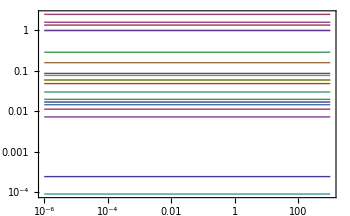

```mathematica
{concSol,fluxSol}=simulate[iABglycolysis,{t,0,1000}];
plotSimulation[concSol]/.m_metabolite:>getID[m]
```

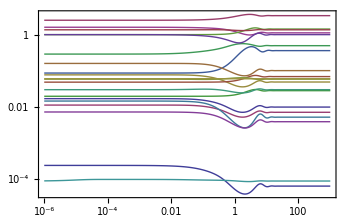

```mathematica
{concSol,fluxSol}=simulate[iABglycolysis,{t,0,1000},Parameters->{Subscript[k, ATP_hydrolysis]^⟶->2 Hour^-1}];
plotSimulation[concSol]/.m_metabolite:>getID[m]
```

### Pentose phosphate pathway

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
ppp=Import["../models/SB2/ppp.m.gz"];
```

```mathematica
sb2ToiAB={"vg6pdh"->"G6PDH2r","vpglase"->"PGL","vgl6pdh"->"GND","vr5pe"->"RPE","vr5pi"->"RPI","vtki"->"TKT1","vtkii"->"TKT2","vtala"->"TALA","vgssgr"->"GTHO","vgshr"->"GTHP"}
```

{vg6pdh→G6PDH2r,vpglase→PGL,vgl6pdh→GND,vr5pe→RPE,vr5pi→RPI,vtki→TKT1,vtkii→TKT2,vtala→TALA,vgssgr→GTHO,vgshr→GTHP}

```mathematica
TableForm[{Cases[ppp["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^vg6pdh | (g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r
((6pgl)^c+h2o^c⇌(6pgc)^c+h^c)^vpglase | ((6pgl)^c+h2o^c→(6pgc)^c+h^c)^PGL
((6pgc)^c+nadp^c⇌co2^c+nadph^c+(ru5p-D)^c)^vgl6pdh | ((6pgc)^c+nadp^c→co2^c+nadph^c+(ru5p-D)^c)^GND
((ru5p-D)^c⇌(xu5p-D)^c)^vr5pe | ((ru5p-D)^c⇌(xu5p-D)^c)^RPE
((ru5p-D)^c⇌r5p^c)^vr5pi | (r5p^c⇌(ru5p-D)^c)^RPI
(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^vtki | (r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1
(e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^vtkii | (e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^TKT2
(g3p^c+s7p^c⇌e4p^c+f6p^c)^vtala | (g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA
(gthox^c+h^c+nadph^c⇌2 gthrd^c+nadp^c)^vgssgr | (gthox^c+h^c+nadph^c→2 gthrd^c+nadp^c)^GTHO
(2 gthrd^c⇌gthox^c+2 h^c)^vgshr | (2 gthrd^c+h2o2^c⇌gthox^c+2 h2o^c)^GTHP

```mathematica
iABppp=subModel[rbc,ppp["Fluxes"]/.sb2ToiAB];
setUnitChecking[iABppp,True];
setID[iABppp,"iAB-RBC-238-PentosePhosphatePathway"];
setIgnore[iABppp,{m["h","c"],m["h2o","c"]}];
iABppp=addSinks[iABppp,{m["f6p","c"],m["g6p","c"],m["g3p","c"],m["h2o","c"],m["h","c"],m["co2","c"],m["h2o2","c"]}];
(*updateBoundaryConditions[iABppp,{m["h","c"],m["h2o","c"]}];*)

ssFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@{Subscript[v, G6PDH2r]->0.21,Subscript[v, GND]->0.21,Subscript[v, GTHO]->0.42,Subscript[v, GTHP]->0.42,Subscript[v, PGL]->0.21,Subscript[v, RPE]->0.13999999999998636,Subscript[v, RPI]->-0.07000000000005002,Subscript[v, TALA]->0.07000000000005002,Subscript[v, TKT1]->0.07000000000005002,Subscript[v, TKT2]->0.07000000000005002,Subscript[v, Sink_f6p[c]]->0.13999999999999999,Subscript[v, Sink_g6p[c]]->-0.21,Subscript[v, Sink_g3p[c]]->0.06999999999999999,Subscript[v, Sink_h2o[c]]->0.63,Subscript[v, Sink_h[c]]->0.,Subscript[v, Sink_co2[c]]->0.21,Subscript[v, Sink_h2o2[c]]->-0.42};
ssConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{g6p^c->0.0486,f6p^c->0.0198,g3p^c->0.00728,(6pgl)^c->0.001754242723,(6pgc)^c->0.037475258,(ru5p-D)^c->0.0049367903,(xu5p-D)^c->0.014784196,r5p^c->0.012668936,s7p^c->0.023987984,e4p^c->0.0050750696,nadp^c->0.0002,nadph^c->0.0658,gthrd^c->3.2,gthox^c->0.11999999999999966,h^c->0.00006309573444801929,h2o2^c->0.00001,h2o^c->1.99999683,co2^c->1.0000021};
setInitialConditions[iABppp,Join[ssFluxes,ssConc]];
setParameters[iABppp,{parameter["Volume", "c"] -> 1 Liter, Keq["Sink_h[c]"] -> 1, Keq["Sink_h2o[c]"] -> 1, Keq["Sink_g6p[c]"] -> 1, Keq["Sink_g3p[c]"] -> ∞,Keq["Sink_h2o2[c]"] -> 1,
Keq["Sink_co2[c]"] -> 1,Keq["Sink_f6p[c]"] -> ∞, Keq["G6PDH2r"] -> 1000, Keq["PGL"] -> 1000, Keq["GND"] -> 1000, Keq["RPE"] -> 3, Keq["RPI"] -> 1/2.57, 
  Keq["TKT1"] -> 3, Keq["TKT2"] -> 10.3, Keq["TALA"] -> 1.05, Keq["GTHO"] -> 100,Keq["GTHP"] -> ∞(*, Keq["GSHR"] -> 2*),h^Xt->0.00006309573444801929 Millimole Liter^-1,co2^Xt->Millimole Liter^-1,g6p^Xt->Millimole Liter^-1,f6p^Xt->Millimole Liter^-1,r5p^Xt->Millimole Liter^-1,h2o^Xt->Millimole Liter^-1,g3p^Xt->Millimole Liter^-1,h2o2^Xt->1Millimole Liter^-1}];
perc=calcPERC[iABppp]/.Undefined->1000000 Hour^-1;
updateParameters[iABppp,perc];
updateNotes[iABppp,defaultInitializationNotes[]<>"\n This model is a translation of the pentose phosphate pathway model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbar."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz",iABppp]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: 1000 Millimole Liter^-1

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: 100 Millimole Liter^-1

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: ∞ Liter^2 Millimole^-2

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::atequilibrium: Reaction "Sink_h[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz

```mathematica
perc
```

{k_G6PDH2r^⟶→21864.6 Liter Hour^-1 Millimole^-1,k_GND^⟶→28018.5 Liter Hour^-1 Millimole^-1,k_GTHO^⟶→53.1915 Liter Hour^-1 Millimole^-1,k_GTHP^⟶→4101.56 Liter^2 Hour^-1 Millimole^-2,k_PGL^⟶→119.71 Hour^-1,k_RPE^⟶→16045.9 Hour^-1,k_RPI^⟶→3760.39 Hour^-1,k_TALA^⟶→886.848 Liter Hour^-1 Millimole^-1,k_TKT1^⟶→542.261 Liter Hour^-1 Millimole^-1,k_TKT2^⟶→1146.86 Liter Hour^-1 Millimole^-1,k_Sink_f6p[c]^⟶→7.07071 Hour^-1,k_Sink_g6p[c]^⟶→0.220727 Hour^-1,k_Sink_g3p[c]^⟶→9.61538 Hour^-1,k_Sink_h2o[c]^⟶→0.630002 Hour^-1,k_Sink_h[c]^⟶→1000000 Hour^-1,k_Sink_co2[c]^⟶→100000. Hour^-1,k_Sink_h2o2[c]^⟶→0.420004 Hour^-1}

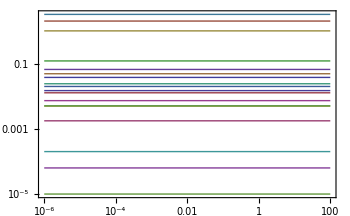

```mathematica
{concSol,fluxSol}=simulate[iABppp,{t,0,100}];
plotSimulation[concSol]
```

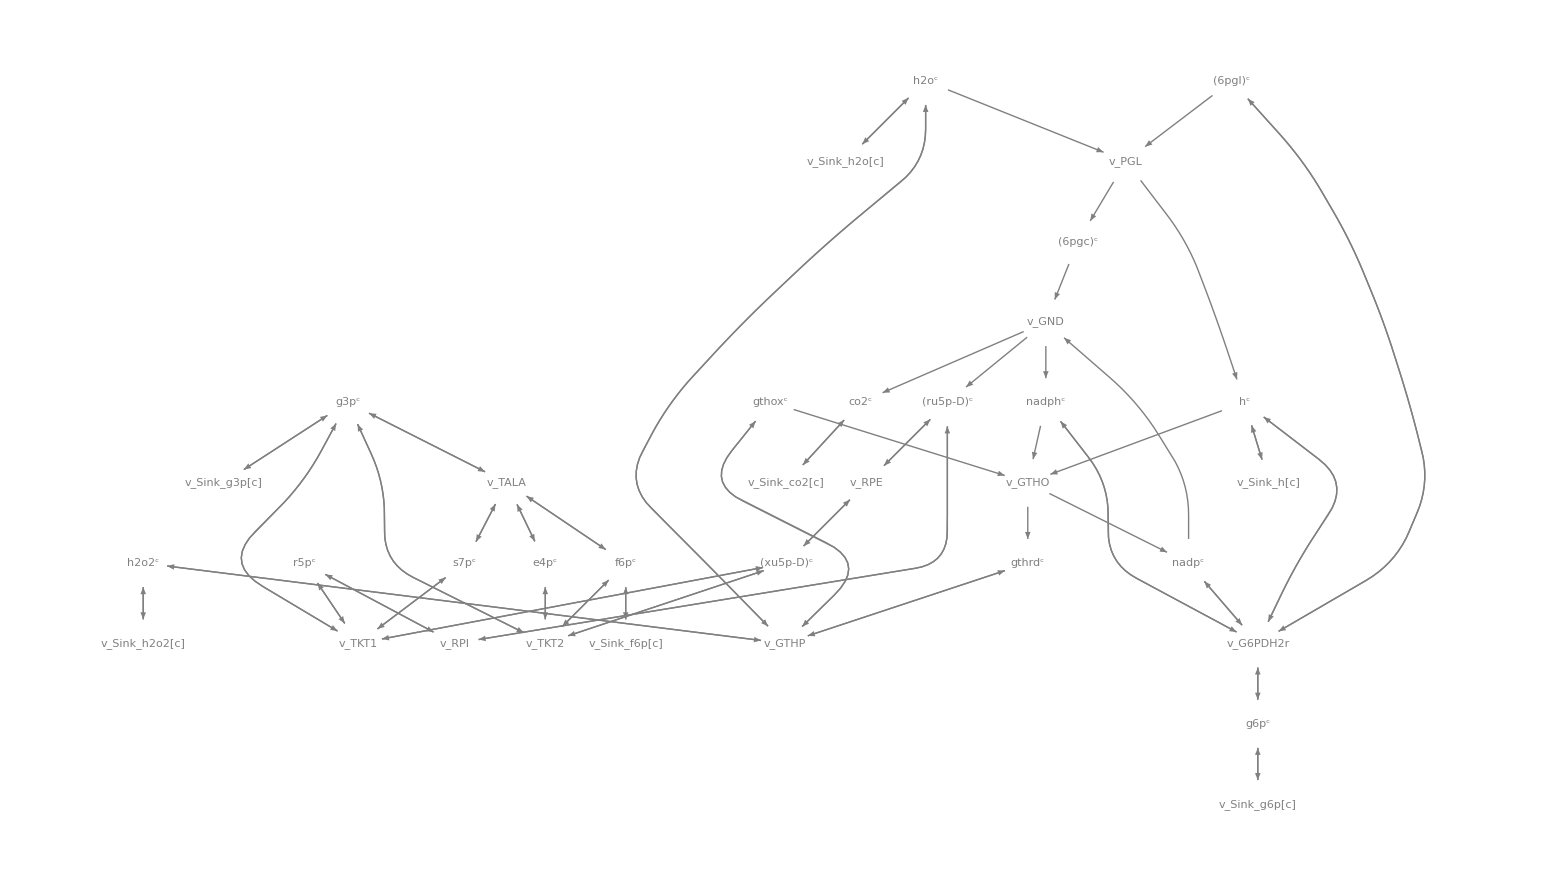

```mathematica
visualizePathways[reactions2bipartite[iABppp["Reactions"]],
DirectedEdges->True,PlotStyle->{GrayLevel[0.5],Arrowheads[.012]},
"MetaboliteRenderingFunction"->({Style[Text[StandardForm@#2,#1],
Background->Opacity[.6,White]]}&),"ReactionRenderingFunction"->({Style[Text[StandardForm@#2,#1],Larger,Background->Opacity[.6,LightGray]]}&),ImageSize->1600,MultiedgeStyle->None]
```

### Nucleotide salvage pathway

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
salvage=Import["../models/SB2/salvage.m.gz"];
```

```mathematica
sb2ToiAB={"vada"->"ADA","vadprt"->"ADPT","vak"->"ADNK1","vampase"->"NTD7","vampda"->"AMPDA","vimpase"->"NTD11","vpnpase"->"PUNP5","vprm"->"PPM","vprppsyn"->"PRPPS"}
```

{vada→ADA,vadprt→ADPT,vak→ADNK1,vampase→NTD7,vampda→AMPDA,vimpase→NTD11,vpnpase→PUNP5,vprm→PPM,vprppsyn→PRPPS}

```mathematica
TableForm[{Cases[salvage["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(adn^c+h2o^c⇌ins^c+nh3^c)^vada | (adn^c+h^c+h2o^c→ins^c+nh4^c)^ADA
(ade^c+h2o^c+prpp^c⇌amp^c+2 pi^c)^vadprt | (ade^c+prpp^c→amp^c+ppi^c)^ADPT
(adn^c+atp^c⇌adp^c+amp^c)^vak | (adn^c+atp^c→adp^c+amp^c+h^c)^ADNK1
(amp^c+h2o^c⇌adn^c+h^c+pi^c)^vampase | (amp^c+h2o^c→adn^c+pi^c)^NTD7
(amp^c+h2o^c⇌imp^c+nh3^c)^vampda | (amp^c+h^c+h2o^c→imp^c+nh4^c)^AMPDA
(h2o^c+imp^c⇌h^c+ins^c+pi^c)^vimpase | (h2o^c+imp^c→ins^c+pi^c)^NTD11
(ins^c+pi^c⇌hxan^c+r1p^c)^vpnpase | (ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5
(r1p^c⇌r5p^c)^vprm | (r1p^c⇌r5p^c)^PPM
(2 atp^c+r5p^c⇌2 adp^c+h^c+prpp^c)^vprppsyn | (atp^c+r5p^c⇌amp^c+h^c+prpp^c)^PRPPS

```mathematica
iABsalvage=subModel[rbc,salvage["Fluxes"]/.sb2ToiAB];
setIgnore[iABsalvage,{m["h","c"],m["h2o","c"]}]
updateUnitChecking[iABsalvage,True]
iABsalvage=addReaction[iABsalvage,Overscript[adp^c+h^c+pi^c⇌atp^c+h2o^c, vatpgen]](*not in BIGG*);
iABsalvage=addSinks[iABsalvage,{m["ade","c"],m["adn","c"],m["hxan","c"],m["ins","c"],m["pi","c"],m["amp","c"],m["h","c"],m["h2o","c"],(*these are new*)m["ppi","c"],m["nh4","c"],m["adp","c"]}];
ssConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{r5p^c->0.00494,ade^c->0.001,adn^c->0.0012,imp^c->0.01,ins^c->0.001,hxan^c->0.002,r1p^c->0.06,prpp^c->0.005,amp^c->0.08672812499999999,adp^c->0.29,atp^c->1.6,pi^c->2.5,ppi^c->0.0015,h^c->0.00006309573444801929,h2o^c->0.99999976,nh4^c->0.091};
ssFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@Chop@fba[iABsalvage,"vatpgen",Join[{"ADA"->{0.01,0.01},"ADNK1"->{0.12,0.12},"vatpgen"->{0,0.148},"NTD11"->{0.014,0.014}},{"Sink_ade[c]"->{-0.014,-0.014},"Sink_adn[c]"->{-∞,0},"Sink_hxan[c]"->{-∞,∞},"Sink_ins[c]"->{-∞,∞},"Sink_pi[c]"->{-∞,∞},"Sink_amp[c]"->{-∞,∞},"Sink_h[c]"->{-∞,-∞},"Sink_h2o[c]"->{0,0},"Sink_ppi[c]"->{-∞,∞},"Sink_nh4[c]"->{-∞,∞},"Sink_adp[c]"->{-∞,∞}}]];
setInitialConditions[iABsalvage,Join[ssConc,ssFluxes]];
xtrnlConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{ppi^Xt->0.0015,adn^Xt->0.0012001,ade^Xt->0.00100014,hxan^Xt->0.00199986,nh4^Xt->0.0909999,amp^Xt->0.09540093749999999,h^Xt->0.0006309573444801929,pi^Xt->0.25,ins^Xt->0.0009999,adp^Xt->0.3,m["h2o","Xt"]->1};
param={Underscript[Volume, c]->Liter,Underscript[K, ADNK1]->1000000,Underscript[K, NTD7]->1000000,Underscript[K, ADA]->1000000,Underscript[K, AMPDA]->1000000,Underscript[K, NTD11]->1000000,Underscript[K, PUNP5]->0.09,Underscript[K, PPM]->13.3,Underscript[K, PRPPS]->1000000,Underscript[K, ADPT]->1000000,Underscript[K, Sink_ade[c]]->1,Underscript[K, Sink_pi[c]]->1,Underscript[K, Sink_adp[c]]->1,Underscript[K, Sink_amp[c]]->1,Underscript[K, Sink_ppi[c]]->100000,Underscript[K, Sink_adn[c]]->0.1,Underscript[K, Sink_ins[c]]->1,Underscript[K, Sink_hxan[c]]->1,Underscript[K, Sink_nh4[c]]->1,Underscript[K, vatpgen]->1000000,Underscript[K, Sink_h[c]]->1,Underscript[K, Sink_h2o[c]]->1};
setParameters[iABsalvage,Join[xtrnlConc,param]];
perc=calcPERC[iABsalvage]/.Undefined->1;
updateParameters[iABsalvage,perc]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed: 1000000 Millimole Liter^-1

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::negativePERC: Negative PERC (-0.016888888888884443` Hour^-1) detected for reaction "Sink_pi[c]".

calcPERC::negativePERC: Negative PERC (-4.381508305408423` Hour^-1) detected for reaction "Sink_amp[c]".

calcPERC::atequilibrium: Reaction "Sink_h2o[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: Hour^-1

```mathematica
perc
```

{k_ADA^⟶→8.33333 Hour^-1,k_ADNK1^⟶→62.5 Liter Hour^-1 Millimole^-1,k_ADPT^⟶→2800. Liter Hour^-1 Millimole^-1,k_AMPDA^⟶→0.161424 Hour^-1,k_NTD11^⟶→1.4 Hour^-1,k_NTD7^⟶→1.10691 Hour^-1,k_PPM^⟶→0.234787 Hour^-1,k_PRPPS^⟶→1.77126 Liter Hour^-1 Millimole^-1,k_PUNP5^⟶→12. Liter Hour^-1 Millimole^-1,k_vatpgen^⟶→0.184828 Liter Hour^-1 Millimole^-1,k_Sink_ade[c]^⟶→100000. Hour^-1,k_Sink_adn[c]^⟶→3.14786 Hour^-1,k_Sink_hxan[c]^⟶→100000. Hour^-1,k_Sink_ins[c]^⟶→100000. Hour^-1,k_Sink_pi[c]^⟶→-0.0168889 Hour^-1,k_Sink_amp[c]^⟶→-4.38151 Hour^-1,k_Sink_h[c]^⟶→42.2638 Hour^-1,k_Sink_h2o[c]^⟶→1,k_Sink_ppi[c]^⟶→9.33343 Hour^-1,k_Sink_nh4[c]^⟶→240000. Hour^-1,k_Sink_adp[c]^⟶→1.4 Hour^-1}

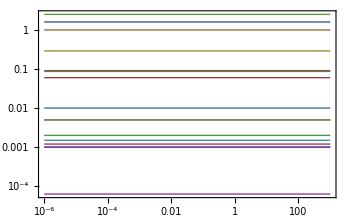

```mathematica
{concSol,fluxSol}=simulate[iABsalvage,{t,0,1000}];
plotSimulation[concSol]
```

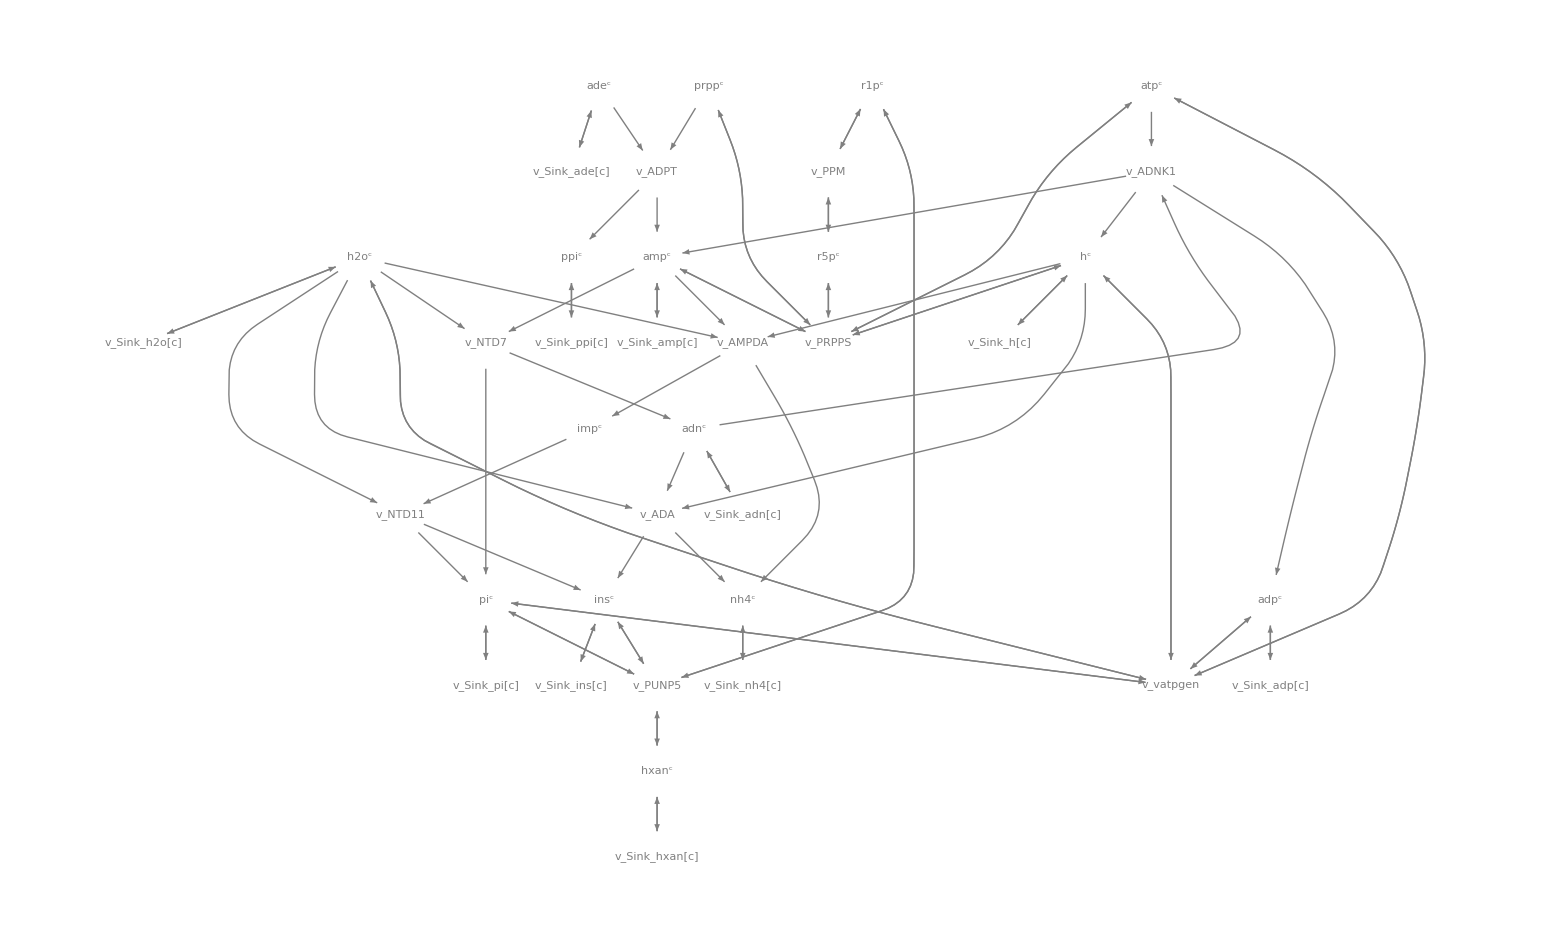

```mathematica
visualizePathways[reactions2bipartite[iABsalvage["Reactions"]],
DirectedEdges->True,PlotStyle->{GrayLevel[0.5],Arrowheads[.012]},
"MetaboliteRenderingFunction"->({Style[Text[StandardForm@#2,#1],
Background->Opacity[.6,White]]}&),"ReactionRenderingFunction"->({Style[Text[StandardForm@#2,#1],Larger,Background->Opacity[.6,LightGray]]}&),ImageSize->1600,MultiedgeStyle->None]
```

```mathematica
elementallyBalancedQ[iABsalvage]
stoichiometricallyConsistentQ[iABsalvage]
```

True

True

```mathematica
updateNotes[iABsalvage,defaultInitializationNotes[]<>"\n This model is a translation of the nucleotide salvage pathway model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbar."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz",iABsalvage]
```

../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz

### Hemoglobin

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
hemoglobin=Import["../models/SB2/Hemoglobin.m.gz"];
```

```mathematica
sb2ToiAB={"vdpgm"->"DPGM","vdpgase"->"DPGase"}
```

{vdpgm→DPGM,vdpgase→DPGase}

```mathematica
TableForm[{Cases[hemoglobin["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

((13dpg)^c⇌(23dpg)^c+h^c)^vdpgm | ((13dpg)^c⇌(23dpg)^c+h^c)^DPGM
((23dpg)^c+h2o^c⇌(3pg)^c+pi^c)^vdpgase | ((23dpg)^c+h2o^c→(3pg)^c+pi^c)^DPGase

```mathematica
iABhemoglobin=subModel[rbc,hemoglobin["Fluxes"]/.sb2ToiAB];
setIgnore[iABhemoglobin,{m["h","c"],m["h2o","c"]}];
iABhemoglobin=addReactions[iABhemoglobin,{Overscript[(23dpg)^c+hb^c⇌dhb^c, vhbdpg],Overscript[hb^c+o2^c⇌hbo2^c, vhbo1],Overscript[hbo2^c+o2^c⇌hbo22^c, vhbo2],Overscript[hbo22^c+o2^c⇌hbo23^c, vhbo3],Overscript[hbo23^c+o2^c⇌hbo24^c, vhbo4],(o2^c⇌∅)^Sink_o2[c]}];
updateInitialConditions[iABhemoglobin,FilterRules[hemoglobin["InitialConditions"]/.sb2MetsToiAB,iABhemoglobin["Species"]]];
updateParameters[iABhemoglobin,hemoglobin["Parameters"]/.sb2ToiAB/."vo2"->"Sink_o2[c]"]
```

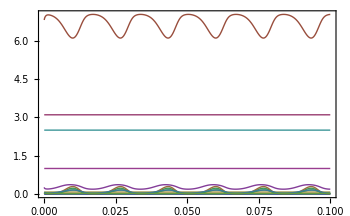

```mathematica
hemoglobinStandalone=iABhemoglobin;
updateBoundaryConditions[hemoglobinStandalone,{(23dpg)^c,(13dpg)^c,(3pg)^c,pi^c,h2o^c,h^c}]
{concSol,fluxSol}=simulate[stripUnits@hemoglobinStandalone,{t,0,.1},Parameters->{m["o2","Xt"]->(30*Cos[120*Pi*t]+70)*0.00028684},MaxSteps->100000];
plotSimulation[concSol,PlotFunction->Plot,Tooltipped->False]
```

```mathematica
updateNotes[iABhemoglobin,defaultInitializationNotes[]<>"\n This model is a translation of the hemoglobin model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbar."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-Hemoglobin.m.gz",iABhemoglobin]
```

../models/iAB-RBC-238/iAB-RBC-238-Hemoglobin.m.gz

### Combinations

```mathematica
o2Saturation={"r_OHb"->(25 (hbo2^c+2 hbo22^c+3 hbo23^c+4 hbo24^c))/(dhb^c+hb^c+hbo2^c+hbo22^c+hbo23^c+hbo24^c)};
```

```mathematica
SetDirectory[NotebookDirectory[]];
iABglycolysis=Import["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz"];
iABppp=Import["../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz"];
iABsalvage=Import["../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz"];
iABhemoglobin=Import["../models/iAB-RBC-238/iAB-RBC-238-Hemoglobin.m.gz"];
```

```mathematica
iABcombi=Union[iABglycolysis,iABsalvage,iABppp,iABhemoglobin];
iABcombi=deleteReactions[iABcombi,{"Sink_g6p[c]","Sink_f6p[c]","Sink_g3p[c]","Sink_amp[c]","vatpgen"}];
updateConstraints[iABcombi,v[getID[#]]->{-∞,∞}&/@getExchanges[iABcombi]]
updateConstraints[iABcombi,{v["Sink_glc-D[c]"]->{-∞,0},v["Sink_lac-L[c]"]->{0,∞},v["Sink_pyr[c]"]->{0,∞}}]
updateParameters[iABcombi,{Keq["Sink_h2o[c]"]->1.1}]
```

```mathematica
fvaSol=Sort@fva[iABcombi,{v["HEX1"]->{1.12,1.12},v["G6PDH2r"]->{0.21},v["DPGM"]->{0.441,0.441},v["PGI"]->{0.91,0.91},v["PFK"]->{1.05,1.05},v["LDH_L"]->{-1.95,-1.95},"ADK1"->{0,0},"ADNK1"->{0.12,0.12},"PRPPS"->{0.014,0.014},"ADA"->{0.01,0.01},"NTD7"->{0.0148,0.0148}}];
plotFVA[%,ImageSize->800];
newSSfluxes=#[[1]]->#[[2,1]]Millimole Liter^-1 Hour^-1&/@fvaSol;
updateInitialConditions[iABcombi,newSSfluxes]
perc=SortBy[Quiet[calcPERC[iABcombi],{calcPERC::atequilibrium,calcPERC::ZeroKeq}],Last];
perc=updateRules[perc,FilterRules[iABhemoglobin["Parameters"],_rateconst]]/.Undefined->100000 Liter Hour^-1 Millimole^-1;
SortBy[perc,Last];
updateParameters[iABcombi,perc]
```

```mathematica
{concSol,fluxSol}=simulate[iABcombi,{t,0,100000}];
```

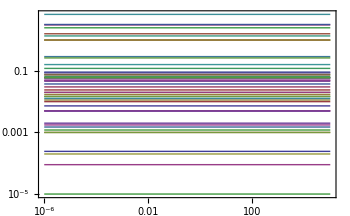

```mathematica
plotSimulation[concSol,Tooltipped->True]
```

```mathematica
{concSolHb,fluxSolHb}=simulate[iABcombi,{t,0,.2},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4}];
```

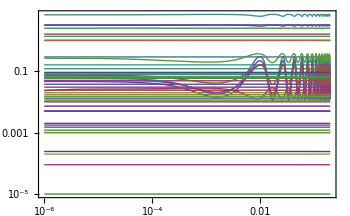

```mathematica
plotSimulation[concSolHb]
```

```mathematica
SlideView[{plotSimulation[o2Saturation/.concSolHb,PlotRange->{All,{80,100}},PlotFunction->Plot,FrameLabel->{"Time [h]","O_2 saturation [%]"}],plotSimulation[filter[fluxSolHb,{Subscript[v, Sink_o2[c]]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Legend->{Bottom,Right}],plotSimulation[FilterRules[fluxSolHb,{Subscript[v, ENO],Subscript[v, PYK]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}],
plotSimulation[FilterRules[fluxSolHb,{Subscript[v, DPGM],Subscript[v, DPGase]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]}]
```

## Hemoglobin

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

### Adair

```mathematica
init=protein["Hb_Oxy","c"];
oxygenationHb=Table[
prod=bind[init,metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
oxygenationHb
```

{(o2^c+Hb_Oxy^c⇌Hb_Oxy^c | o2^c)^(protein_Hb_Oxy & o2[c] + o2[c]),(Hb_Oxy^c | o2^c+o2^c⇌Hb_Oxy^c | 2 o2^c)^(protein_Hb_Oxy & 2 o2[c] + o2[c]),(Hb_Oxy^c | 2 o2^c+o2^c⇌Hb_Oxy^c | 3 o2^c)^(protein_Hb_Oxy & 3 o2[c] + o2[c]),(Hb_Oxy^c | 3 o2^c+o2^c⇌Hb_Oxy^c | 4 o2^c)^(protein_Hb_Oxy & 4 o2[c] + o2[c])}

```mathematica
adairHb=constructModel[oxygenationHb];
```

### MWC

```mathematica
init=protein["Hb_Oxy","c"];
oxygenationHb=Table[
prod=bind[init,metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
init=protein["Hb_Deoxy","c"];
oxygenationDHb=Table[
prod=bind[init,metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
transition=Table[
substr=complex[protein["Hb_Deoxy","c"],Sequence@@Table[o2^c,{i}]];
prod=complex[protein["Hb_Oxy","c"],Sequence@@Table[o2^c,{i}]];
rxn=r[ToString[substr]<>" <=> " <>ToString[prod],{substr},{prod},{1,1}];
(*rxn=r["T2R_"<>ToString[i],{substr},{prod},{1,1}];*)
init=prod;
rxn
,{i,1,4}];
```

```mathematica
hb=constructModel[Join[oxygenationHb,oxygenationDHb,transition]];
```

```mathematica
hb
```

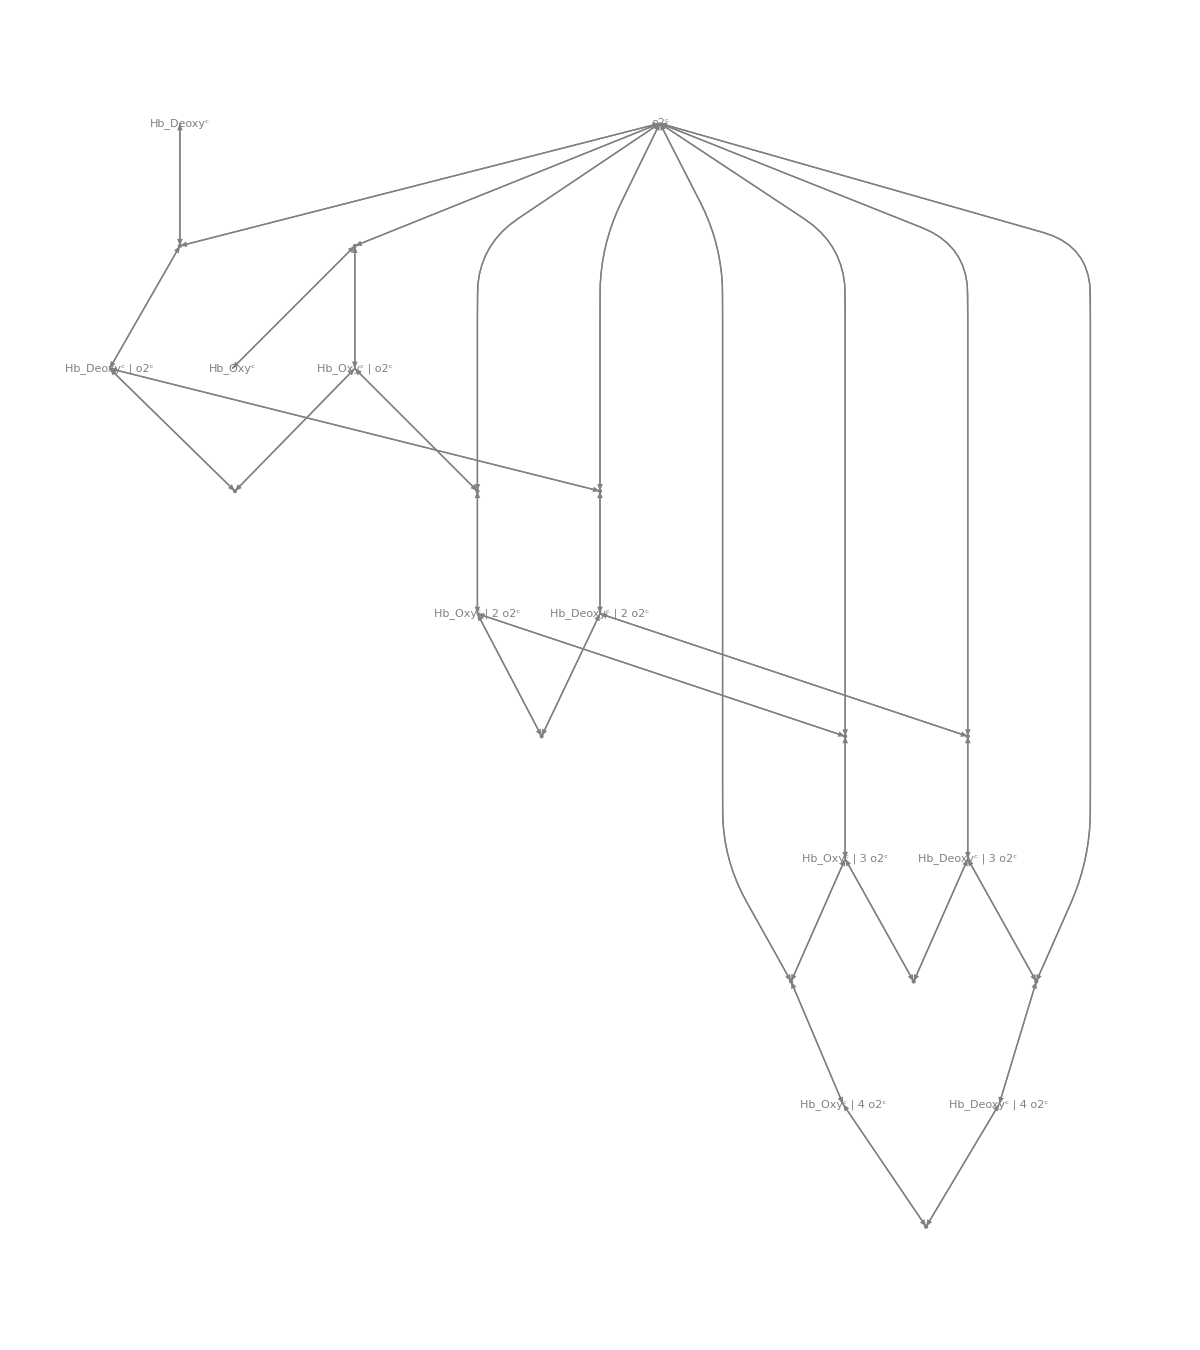

```mathematica
visualizePathways[hb,"MetaboliteRenderingFunction"->(Text[StandardForm[#2],#1]&),"ReactionRenderingFunction"->(Point[#1]&),ImageSize->1200]
```